# Brendan Philbin Thermal Annealing Analysis

## Trial 1 (no annealing): N=32, M=100, R=100, J=2, S=3, C=4, β=5

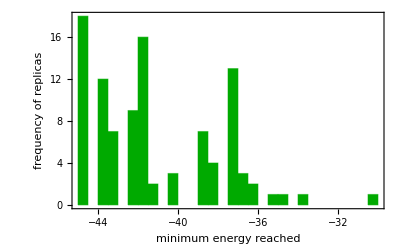

```mathematica
SetDirectory[NotebookDirectory[]];
trial1=Flatten[Import["histogram1.csv","CSV"]];
Histogram[trial1,100,ChartStyle->Darker[Green],Frame->True,FrameLabel->{"minimum energy reached","frequency of replicas"}]
```

## Trial 2 (no annealing): N=32, M=200, R=100, J=2, S=4, C=5, β=5

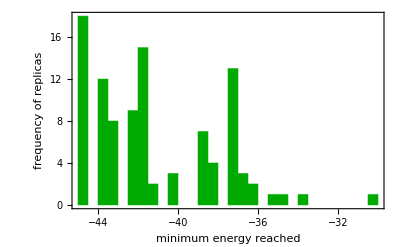

```mathematica
trial2=Flatten[Import["histogram2.csv","CSV"]];
Histogram[trial2,100,ChartStyle->Darker[Green],Frame->True,FrameLabel->{"minimum energy reached","frequency of replicas"}]
```

## Trial 3 (no annealing): N=32, M=400, R=100, J=2, S=5, C=6, β=5

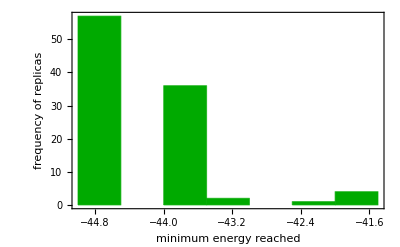

```mathematica
trial3=Flatten[Import["histogram3.csv","CSV"]];
Histogram[trial3,100,ChartStyle->Darker[Green],Frame->True,FrameLabel->{"minimum energy reached","frequency of replicas"}]
```

## Trial 4 (w/ annealing): N=32, M=100, R=100, J=2, S=3, C=4, β=5

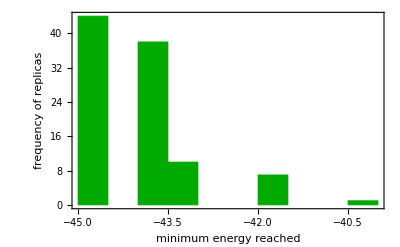

```mathematica
trial4=Flatten[Import["histogram4.csv","CSV"]];
Histogram[trial4,100,ChartStyle->Darker[Green],Frame->True,FrameLabel->{"minimum energy reached","frequency of replicas"}]
```

## Trial 5 (w/ annealing): N=32, M=200, R=100, J=2, S=4, C=5, β=5

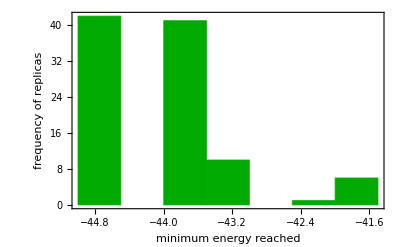

```mathematica
trial5=Flatten[Import["histogram5.csv","CSV"]];
Histogram[trial5,100,ChartStyle->Darker[Green],Frame->True,FrameLabel->{"minimum energy reached","frequency of replicas"}]
```

## Trial 6 (w/ annealing): N=32, M=400, R=100, J=2, S=5, C=6, β=5

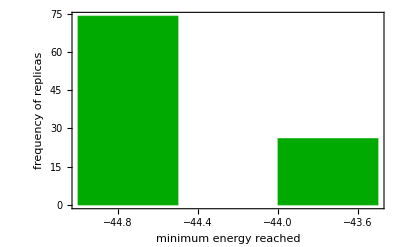

```mathematica
trial6=Flatten[Import["histogram6.csv","CSV"]];
Histogram[trial6,100,ChartStyle->Darker[Green],Frame->True,FrameLabel->{"minimum energy reached","frequency of replicas"}]
```